## BHZ Model

```mathematica
Clear["Global`*"];
hBHZ[kx_,ky_,cc_]:=Module[{ham,s0,sz,sx,sy,h1,h2,coup},
s0=IdentityMatrix[2];
sz=PauliMatrix[3];
sx=PauliMatrix[1];
sy=PauliMatrix[2];
h1=(u+Cos[kx]+Cos[ky])*sz+Sin[ky]*sy;
h2=Sin[kx]*sx;
coup=cc*sy;
ham=KroneckerProduct[s0,h1]+KroneckerProduct[sz,h2]+KroneckerProduct[sx,coup];
Return[ham];
]
TrigToExp@hBHZ[kx,ky,0.3]//MatrixForm
```

((0.+0. ⅈ)+ⅇ^(-ⅈ kx)/2+ⅇ^(ⅈ kx)/2+ⅇ^(-ⅈ ky)/2+ⅇ^(ⅈ ky)/2+u | (0.+0. ⅈ)+1/2 ⅈ ⅇ^(-ⅈ kx)-1/2 ⅈ ⅇ^(ⅈ kx)+ⅇ^(-ⅈ ky)/2-ⅇ^(ⅈ ky)/2 | 0.+0. ⅈ | 0.-0.3 ⅈ
(0.+0. ⅈ)+1/2 ⅈ ⅇ^(-ⅈ kx)-1/2 ⅈ ⅇ^(ⅈ kx)-ⅇ^(-ⅈ ky)/2+ⅇ^(ⅈ ky)/2 | (0.+0. ⅈ)-ⅇ^(-ⅈ kx)/2-ⅇ^(ⅈ kx)/2-ⅇ^(-ⅈ ky)/2-ⅇ^(ⅈ ky)/2-u | 0.+0.3 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.-0.3 ⅈ | (0.+0. ⅈ)+ⅇ^(-ⅈ kx)/2+ⅇ^(ⅈ kx)/2+ⅇ^(-ⅈ ky)/2+ⅇ^(ⅈ ky)/2+u | (0.+0. ⅈ)-1/2 ⅈ ⅇ^(-ⅈ kx)+1/2 ⅈ ⅇ^(ⅈ kx)+ⅇ^(-ⅈ ky)/2-ⅇ^(ⅈ ky)/2
0.+0.3 ⅈ | 0.+0. ⅈ | (0.+0. ⅈ)-1/2 ⅈ ⅇ^(-ⅈ kx)+1/2 ⅈ ⅇ^(ⅈ kx)-ⅇ^(-ⅈ ky)/2+ⅇ^(ⅈ ky)/2 | (0.+0. ⅈ)-ⅇ^(-ⅈ kx)/2-ⅇ^(ⅈ kx)/2-ⅇ^(-ⅈ ky)/2-ⅇ^(ⅈ ky)/2-u)

```mathematica
Plot3D[Sort@Eigenvalues[hBHZ[kx,ky,0.2]/.{u->0.}],{kx,-π,π},{ky,-π,π},Mesh->None,ColorFunction->"RedGreenSplit",AxesLabel->{kx,ky,Energy},BoxRatios->{1,1,1.5},PlotStyle->Opacity[0.75]]
```

-Graphics3D-

```mathematica
Clear[stripHamBHZ];
stripHamBHZ[ky_,num_]:=Module[{ham,h00,h01,h10,hxx,hyy,hu,s0,sx,sy,sz},
Thread[{s0,sx,sy,sz}=Table[PauliMatrix[i],{i,{0,1,2,3}}]];
hxx=KroneckerProduct[1/2 s0,sz]+KroneckerProduct[ⅈ/2 sz,sx];
hyy=KroneckerProduct[1/2 s0,sz]+KroneckerProduct[ⅈ/2 s0,sy];
h00=KroneckerProduct[DiagonalMatrix[Table[1,num-1],1],hxx]+KroneckerProduct[DiagonalMatrix[Table[1,num-1],-1],ConjugateTranspose@hxx];
h01=KroneckerProduct[DiagonalMatrix[Table[1,num]],hyy]*Exp[-ⅈ ky];
h10=KroneckerProduct[DiagonalMatrix[Table[1,num]],ConjugateTranspose@hyy]*Exp[ⅈ ky];
hu=KroneckerProduct[DiagonalMatrix[Table[1,num]],KroneckerProduct[u s0,sz]+KroneckerProduct[A sx,sy]];
ham=h00+h01+h10+hu;
Return[ham];
]
(*stripHamBHZ[ky,5]//MatrixForm*)
```

```mathematica
hk=stripHamBHZ[ky,10]//Normal;
el=ParallelTable[Sort@Eigenvalues[hk/.{ky->kk,u->-1.2,A->0.3}],{kk,-π,π,0.01*π}];
```

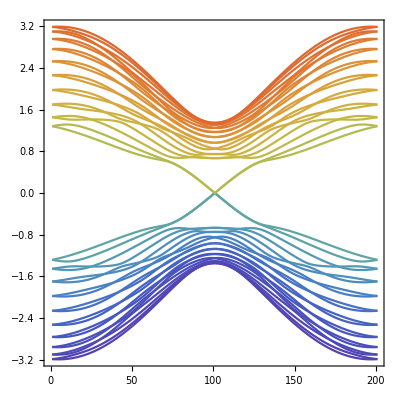

```mathematica
ListPlot[Transpose@Re[el],PlotRange->All,Joined->True,AspectRatio->1,Frame->True,ColorFunction->"Rainbow"]
```

```mathematica
Clear["Global`*"]
```